# Chi distribution

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
http://www.eugenedeon.com/hitchhikers

## Definition

```mathematica
Chi`pc[s_,a_]:=(2^(1-a) ⅇ^(-s^2/4) s^(a-1))/Gamma[a/2]
```

### Normalization

```mathematica
Integrate[Chi`pc[s,a],{s,0,Infinity},Assumptions->a>0]
```

1

### Mean

```mathematica
Integrate[Chi`pc[s,a]s,{s,0,Infinity},Assumptions->a>0]
```

(2 Gamma[(1+a)/2])/Gamma[a/2]

### Moments

```mathematica
Table[Integrate[Chi`pc[s,a] s^p,{s,0,Infinity},Assumptions->a>0&&m>0],{p,{2,3,4,m}}]
```

{2 a,(8 Gamma[(3+a)/2])/Gamma[a/2],4 a (2+a),(2^m Gamma[(a+m)/2])/Gamma[a/2]}

## Laplace transform

```mathematica
LaplaceTransform[Chi`pc[s,a],s,q]
```

(2^(1-a) Gamma[a] HypergeometricU[a/2,1/2,q^2])/Gamma[a/2]

## GRT Statistics

```mathematica
Chi`Xc[s_,a_]:=Gamma[a/2,s^2/4]/Gamma[a/2]
```

```mathematica
Chi`Σtc[s_,a_]:=(2 ⅇ^(-s^2/4))/(s ExpIntegralE[1-a/2,s^2/4])
```

```mathematica
Chi`pu[s_,a_]:=Gamma[a/2,s^2/4]/(2 Gamma[(1+a)/2])
```

```mathematica
Chi`Xu[s_,a_]:=(-s Gamma[a/2,s^2/4]+2 Gamma[(1+a)/2,s^2/4])/(2 Gamma[(1+a)/2])
```

```mathematica
Chi`Σtu[s_,a_]:=1/(-s+(2 Gamma[(1+a)/2,s^2/4])/Gamma[a/2,r^2/4])
```

```mathematica
TableForm[Table[FullSimplify[FunctionExpand[{"a="<>ToString[a],Chi`pc[s,a],Chi`Xc[s,a],Chi`pu[s,a],Chi`Xu[s,a]}],Assumptions->s>0],{a,Range[5]}]]
```

a=1 | (ⅇ^(-s^2/4))/(√π) | Erfc[s/2] | 1/2 √π Erfc[s/2] | ⅇ^(-s^2/4)-1/2 √π s Erfc[s/2]
a=2 | 1/2 ⅇ^(-s^2/4) s | ⅇ^(-s^2/4) | (ⅇ^(-s^2/4))/(√π) | Erfc[s/2]
a=3 | (ⅇ^(-s^2/4) s^2)/(2 √π) | (ⅇ^(-s^2/4) s)/(√π)+Erfc[s/2] | 1/4 (ⅇ^(-s^2/4) s+√π Erfc[s/2]) | ⅇ^(-s^2/4)-1/4 √π s Erfc[s/2]
a=4 | 1/8 ⅇ^(-s^2/4) s^3 | 1/4 ⅇ^(-s^2/4) (4+s^2) | (ⅇ^(-s^2/4) (4+s^2))/(6 √π) | (ⅇ^(-s^2/4) s)/(3 √π)+Erfc[s/2]
a=5 | (ⅇ^(-s^2/4) s^4)/(12 √π) | (ⅇ^(-s^2/4) s (6+s^2))/(6 √π)+Erfc[s/2] | 1/32 (ⅇ^(-s^2/4) s (6+s^2)+6 √π Erfc[s/2]) | 1/16 (ⅇ^(-s^2/4) (16+s^2)-3 √π s Erfc[s/2])

## Fourier Propagator

```mathematica
assumps=a>1;
πd[d,Chi`pc[r,a]]
```

Hypergeometric1F1[a/2,d/2,-z^2]

### special case a = d:

```mathematica
FullSimplify[Hypergeometric1F1[a/2,d/2,-z^2]/.d->a]
```

ⅇ^(-z^2)

## Random Variates / Importance Sampling

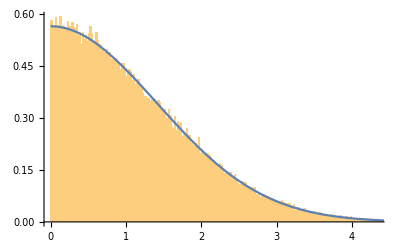

```mathematica
Show[
Histogram[Table[√2 Abs[RandomVariate[NormalDistribution[]]],{i,Range[100000]}],250,"PDF"],
Plot[Chi`pc[s,1],{s,0,6}]
]
```

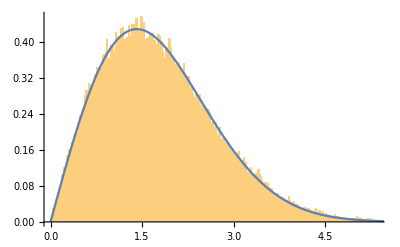

```mathematica
Show[
Histogram[Table[1.12(Abs[RandomVariate[NormalDistribution[]]]+Abs[RandomVariate[NormalDistribution[]]]),{i,Range[100000]}],250,"PDF"],
Plot[Chi`pc[s,2],{s,0,6}]
]
```

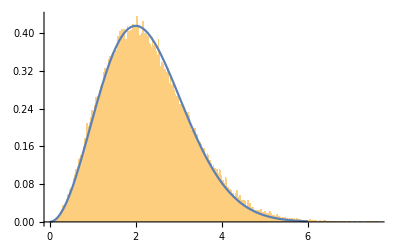

```mathematica
Show[
Histogram[Table[.95(Abs[RandomVariate[NormalDistribution[]]]+Abs[RandomVariate[NormalDistribution[]]]+Abs[RandomVariate[NormalDistribution[]]]),{i,Range[100000]}],250,"PDF"],
Plot[Chi`pc[s,3],{s,0,6}]
]
```

## Singular Eigenfunctions

```mathematica
c/2 Integrate[Exp[t u/v]Chi`pc[t,a],{t,0,Infinity},Assumptions->v>0&&-1<u<1&&a>0]
```

1/2 c (Hypergeometric1F1[a/2,1/2,u^2/v^2]+(2 u Gamma[(1+a)/2] Hypergeometric1F1[(1+a)/2,3/2,u^2/v^2])/(v Gamma[a/2]))

```mathematica
FullSimplify[Table[1/2 c (Hypergeometric1F1[a/2,1/2,u^2/v^2]+(2 u Gamma[(1+a)/2] Hypergeometric1F1[(1+a)/2,3/2,u^2/v^2])/(v Gamma[a/2])),{a,Range[5]}],Assumptions->-1<u<1&&v>1]
```

{1/2 c ⅇ^(u^2/v^2) (1+Erf[u/v]),(c (v+ⅇ^(u^2/v^2) √π u (1+Erf[u/v])))/(2 v),(c ((2 u v)/(√π)+ⅇ^(u^2/v^2) (2 u^2+v^2) (1+Erf[u/v])))/(2 v^2),(2 c v (u^2+v^2)+c ⅇ^(u^2/v^2) √π u (2 u^2+3 v^2) (1+Erf[u/v]))/(4 v^3),(c (4 u^3 v+10 u v^3+ⅇ^(u^2/v^2) √π (4 u^4+12 u^2 v^2+3 v^4) (1+Erf[u/v])))/(6 √π v^4)}

## Grosjean F functions

### a = 1

```mathematica
pc=c Chi`pc[#,1]&
```

c Chi`pc[#1,1]&

```mathematica
Fpc[0,0,pc,z]
```

(c √π Erf[z])/(2 z)

```mathematica
Fpc[1,0,pc,z]
```

(c (z-DawsonF[z]))/(√π z^2)

```mathematica
Fpc[1,1,pc,z]
```

-(2 c ⅇ^(-z^2) z-c √π Erf[z])/(4 z^3)

```mathematica
Fpc[2,0,pc,z]
```

(c ⅇ^(-z^2) (6 z+ⅇ^(z^2) √π (-3+2 z^2) Erf[z]))/(8 z^3)

```mathematica
Fpc[2,1,pc,z]
```

(c (3 z-(3+2 z^2) DawsonF[z]))/(2 √π z^4)

```mathematica
Fpc[2,2,pc,z]
```

(c ⅇ^(-z^2) (-6 z (9+2 z^2)+ⅇ^(z^2) √π (27-12 z^2+4 z^4) Erf[z]))/(32 z^5)

```mathematica
Fpc[k,0,pc,z]
```

1/2 c z^k Gamma[(1+k)/2] Hypergeometric1F1Regularized[(1+k)/2,3/2+k,-z^2]

```mathematica
Fpc[k,1,pc,z]
```

ConditionalExpression[1/4 c z^(-1+k) Gamma[k/2] (2 Hypergeometric1F1Regularized[k/2,1/2+k,-z^2]-(1+k) Hypergeometric1F1Regularized[k/2,3/2+k,-z^2]),k>0]

### a = 2

```mathematica
pc=c Chi`pc[#,2]&
```

c Chi`pc[#1,2]&

```mathematica
Fpc[0,0,pc,z]
```

(c DawsonF[z])/z

```mathematica
Fpc[1,0,pc,z]
```

(c (-2 ⅇ^(-z^2) √π z+π Erf[z]))/(4 z^2)

```mathematica
Fpc[1,1,pc,z]
```

(c (-z+(1+z^2) DawsonF[z]))/z^3

```mathematica
Fpc[2,0,pc,z]
```

(c (3 z-(3+2 z^2) DawsonF[z]))/(2 z^3)

```mathematica
Fpc[2,1,pc,z]
```

-(c (2 ⅇ^(-z^2) √π z (9+4 z^2)+π (-9+2 z^2) Erf[z]))/(16 z^4)

```mathematica
Fpc[2,2,pc,z]
```

(c (-9 z+(9+6 z^2+2 z^4) DawsonF[z]))/(2 z^5)

```mathematica
Fpc[k,0,pc,z]
```

1/2 c √π z^k Gamma[1+k/2] Hypergeometric1F1Regularized[1+k/2,3/2+k,-z^2]

```mathematica
Fpc[k,1,pc,z]
```

1/8 c √π z^(-1+k) Gamma[(1+k)/2] (2 Hypergeometric1F1Regularized[(1+k)/2,1/2+k,-z^2]-Hypergeometric1F1Regularized[(1+k)/2,3/2+k,-z^2]-(1+k) z^2 Hypergeometric1F1Regularized[(3+k)/2,5/2+k,-z^2])

### a = 3

```mathematica
pc=c Chi`pc[#,3]&
```

c Chi`pc[#1,3]&

```mathematica
Fpc[0,0,pc,z]
```

c ⅇ^(-z^2)

```mathematica
Fpc[1,0,pc,z]
```

(c (-z+DawsonF[z]+2 z^2 DawsonF[z]))/(√π z^2)

```mathematica
Fpc[1,1,pc,z]
```

(c (2 ⅇ^(-z^2) (z+z^3)-√π Erf[z]))/(2 z^3)

```mathematica
Fpc[2,0,pc,z]
```

(c ⅇ^(-z^2) (-6 z-4 z^3+3 ⅇ^(z^2) √π Erf[z]))/(4 z^3)

```mathematica
Fpc[2,1,pc,z]
```

(c (-z (9+2 z^2)+(9+8 z^2+4 z^4) DawsonF[z]))/(2 √π z^4)

```mathematica
Fpc[2,2,pc,z]
```

(c ⅇ^(-z^2) (54 z+24 z^3+8 z^5+3 ⅇ^(z^2) √π (-9+2 z^2) Erf[z]))/(8 z^5)

```mathematica
Fpc[l,0,pc,z]
```

c z^l Gamma[(3+l)/2] Hypergeometric1F1Regularized[(3+l)/2,3/2+l,-z^2]

```mathematica
Fpc[l,1,pc,z]
```

1/4 c l z^(-1+l) Gamma[l/2] (2 Hypergeometric1F1Regularized[1+l/2,1/2+l,-z^2]-(1+l) Hypergeometric1F1Regularized[1+l/2,3/2+l,-z^2])

```mathematica
Fpc[l,2,pc,z]
```

1/8 c z^(-2+l) Gamma[(1+l)/2] ((3 (-1+l) l-4 (-2+l) z^2+8 z^4) Hypergeometric1F1Regularized[(1+l)/2,3/2+l,-z^2]-2 (2+l) z^2 (3+2 z^2) Hypergeometric1F1Regularized[(1+l)/2,5/2+l,-z^2])

### General k

```mathematica
Fpc[l,0,c Chi`pc[#,a]&,u]
```

ConditionalExpression[(c √π u^l Gamma[(a+l)/2] Hypergeometric1F1Regularized[(a+l)/2,3/2+l,-u^2])/(2 Gamma[a/2]),l+Re[a]>0]